# KatjaDellaLibera/StickyDBSCAN

Determine fission-fusion dynamics from position data

## Paclet Manifest

"Documentation"

"Kernel"

"StickyDBSCAN.wl"KernelStickyDBSCAN.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

### Basic Description

Paclet publishing the "sticky" DBSCAN-modification used in the animal behaviour paper "Rate of fission-fusion events in domestic sheep is linked to time of day but not resource distribution". The first function "StickyDBSCAN" allows a user to assign groups based on GPS (or other coordinate) data for a number of individuals and time steps. The second function "FindFissionFusionGraph" takes the output of DBSCAN and turns it into a graph that associates groups with overlapping membership if they exist in consecutive time steps.

### Details

Additional information about the paclet.

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["KatjaDellaLibera`StickyDBSCAN`"];
```

### Basic Examples

Sample 5 Brownian Motion paths. We will use this as mock GPS data for 5 individuals:

```mathematica
samples=Table[Transpose[RandomFunction[WienerProcess[], {0,1,.01},2]["States"]],5];
```

Visualize the Paths:

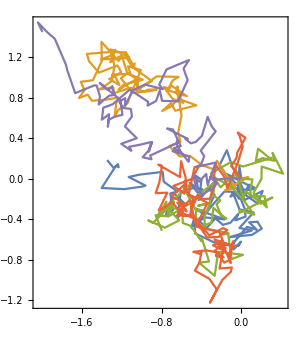

```mathematica
ListLinePlot[samples,ImageSize->300,Axes->None,AspectRatio->Automatic,Frame->True]
```

Make a list of all the pairs:

```mathematica
allBrownianPairs = Table[{a,b},{a,1,Length[samples]},{b,a+1,Length[samples]}]
```

{{{1,2},{1,3},{1,4},{1,5}},{{2,3},{2,4},{2,5}},{{3,4},{3,5}},{{4,5}},{}}

For each of these pairs find the distance at every time step:

```mathematica
allBrownianPairData=Map[Table[EuclideanDistance[samples[[#[[1]],t]],samples[[#[[2]],t]]],{t,1,Length[samples[[1]]]}]&,allBrownianPairs,{2}];
```

Use the stickyDBSCAN function to find the groups at each time step. Let's try an inner radius of 0.3 and an outer radius of 0.5. the tmin is 1 to start from the beginning and the tmax is the number of fake GPS data points:

```mathematica
brownianDBSCAN=StickyDBSCAN[allBrownianPairData,{0.3,0.5},{1,Length[samples[[1]]]},samples];
```

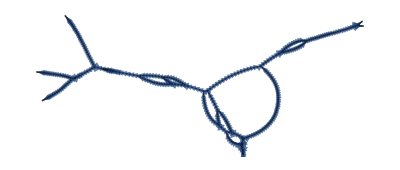

```mathematica
ffGraph=FindFissionFusionGraph[1,Length[samples[[1]]],brownianDBSCAN]
```

We can make the graph look nicer by putting time on the x-axis:

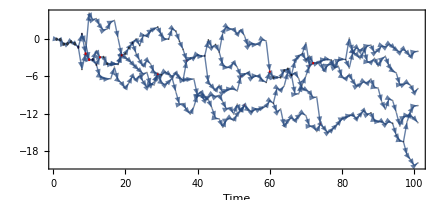

```mathematica
With[{g =ffGraph},
HighlightGraph[Graph[g,
VertexSize->(#->Length[First[#]]*10&/@VertexList[g]),
VertexCoordinates->(#->{Last[#],10*Mean[DeleteMissing[samples[[#[[1]],Last[#],1]]]]}&/@VertexList[g]),Frame->{{False,False},{True,False}},FrameLabel->Style["Time",20],FrameTicks->Automatic],
{Select[VertexList[g],VertexInDegree[g,#]>=2&],Style[Select[VertexList[g],VertexOutDegree[g,#]>=2&],Blue]}]]
```

We can try out a different combination of radii to see fewer fission-fusion events:

```mathematica
brownianDBSCAN2=StickyDBSCAN[allBrownianPairData,{0.1,0.6},{1,Length[samples[[1]]]},samples];
```

```mathematica
ffGraph2=FindFissionFusionGraph[1,Length[samples[[1]]],brownianDBSCAN2];
```

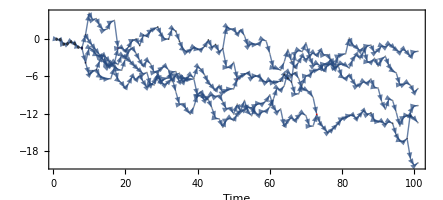

```mathematica
With[{g =ffGraph2},
HighlightGraph[Graph[g,
VertexSize->(#->Length[First[#]]*5&/@VertexList[g]),
VertexCoordinates->(#->{Last[#],10*Mean[DeleteMissing[samples[[#[[1]],Last[#],1]]]]}&/@VertexList[g]),Frame->{{False,False},{True,False}},FrameLabel->Style["Time",20],FrameTicks->Automatic],
{Select[VertexList[g],VertexInDegree[g,#]>=2&],Style[Select[VertexList[g],VertexOutDegree[g,#]>=2&],Blue]}]]
```

## Source & Additional Information

### Creator

Katja Della Libera

### Source Control Repository

https://github.com/katjadellalibera/StickyDBSCAN

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

animal behavior

time series processing

fission-fusion behavior

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

Source, reference or citation

### Links

Link to other related material

### Compatibility

#### Wolfram Language Version

13.2+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

WL system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

WL built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.